# Disk Velocity

## Parameters

```mathematica
GravConstant = 4.300*10^-6
h = 8.9
rho00 = 0.31*10^9
epsdisk = 5.0
z0 = 0.2*h
R = 4*h
delta = 0.2*h
RplusD = R+delta
```

4.3×10^-6

8.9

3.1×10^8

5.

1.78

35.6

1.78

37.38

## Definitions

```mathematica
xparam[r_,u_,z_]:= (r^2+u^2+z^2)/(2*r*u);
px[r_,u_,z_]:= xparam[r,u,z] - Sqrt[xparam[r,u,z]^2-1];
```

## Density Distribution

Piecewise[{{3.1×10^8 ⅇ^(-0.11236 r), r<35.6}, {5.67785×10^6 (1-0.561798 (-35.6+r)), 35.6≤r<37.38}, {0, True}}]

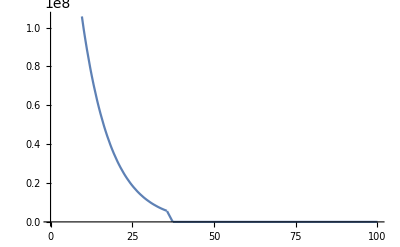

```mathematica
rhozero[r_]:=Piecewise[{{rho00*Exp[-r/h],r<R},
					{rho00*Exp[-R/h]*(1-(r-R)/delta),R <=r<RplusD},
					{0,r≥RplusD}}]
Piecewise[{{rho00*Exp[-r/h],r<R},
		{rho00*Exp[-R/h]*(1-(r-R)/delta),R <=r<RplusD},
		{0,r≥RplusD}}]
Plot[rhozero[r],{r,0,100}]
```

## Partial Derivative of the Density Distribution

```mathematica
durhozero[r_]:=Piecewise[{{-(1/h)*rho00*Exp[-r/h],r<R},
						{-(1/delta)*rho00*Exp[-R/h],R <=r<RplusD},
						{0,r≥RplusD}}]
```

Piecewise[{{-3.48315×10^7 ⅇ^(-0.11236 r), r<35.6}, {-3.1898×10^6, 35.6≤r<37.38}, {0, True}}]

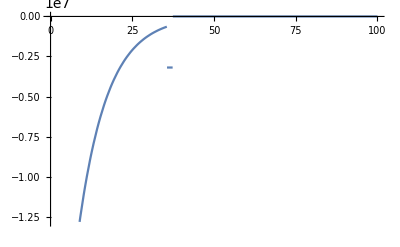

```mathematica
Piecewise[{{-(1/h)*rho00*Exp[-r/h],r<R},
		{-(1/delta)*rho00*Exp[-R/h],R <=r<RplusD},
		{0,r≥RplusD}}]
Plot[durhozero[r],{r,0,100}]
```

## Disk Density Distribution

```mathematica
rhorz[r_,z_]:=rhozero[r]*Cosh[z/z0]^-2
drhorz[r_,z_]:=durhozero[r]*Cosh[z/z0]^-2
```

```mathematica
Plot3D[rhorz[r,z],{r,0,100},{z,-5,5}]
Plot3D[drhorz[r,z],{r,0,100},{z,-5,5}]
```

-Graphics3D-

-Graphics3D-

## Complete Elliptic Integral

```mathematica
kelliptic[r_,u_,z_] := EllipticK[px[r,u,z]]-EllipticE[px[r,u,z]]
```

```mathematica
Plot3D[kelliptic[r,u,5],{r,0,100},{u,0,100}]
```

-Graphics3D-

## Inner Function

```mathematica
innerfunction[r_,u_,z_]:=(2*Sqrt[u]*kelliptic[r,u,z]*drhorz[r,z])/(Pi*Sqrt[r*px[r,u,z]])
```

```mathematica
Plot3D[innerfunction[r,u,1],{r,0,100},{u,0,50}]
```

-Graphics3D-

## Change Order of Variables

```mathematica
innerfunction2[z_,r_,u_]:=innerfunction[r,u,z]
```

```mathematica
Plot3D[innerfunction2[1,r,u],{r,0,100},{u,0,50}]
```

-Graphics3D-

## Inner Integral

```mathematica
innerintegral[r_?NumericQ,u_?NumericQ]:= NIntegrate[innerfunction2[z,r,u],{z,0,Infinity}]
```

```mathematica
Plot3D[innerintegral[r,u],{r,0,100},{u,0,100}]
```

-Graphics3D-

## Change Order of Variables

```mathematica
innerintegral2[u_,r_]:=innerintegral[r,u]
```

```mathematica
Plot3D[innerintegral2[u,r],{r,0,100},{u,0,50}]
```

-Graphics3D-

## Outer Integral

```mathematica
outerintegral[r_?NumericQ]:=NIntegrate[innerintegral2[u,r],{u,0,500}]
```

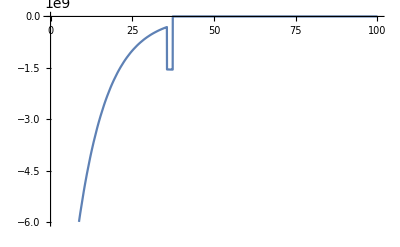

```mathematica
Plot[outerintegral[r],{r,0,100}]
```

## Radial Function

```mathematica
radialforce[r_?NumericQ]:=4*Pi*GravConstant*outerintegral[r]
```

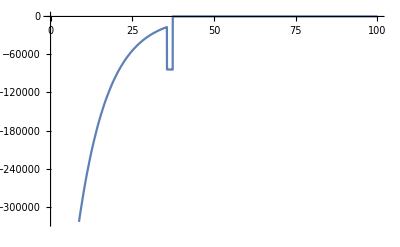

```mathematica
Plot[radialforce[r],{r,0,100}]
```

## Disk Velocity

```mathematica
diskvelocity[r_]:=Sqrt[-r*radialforce[r]]
```

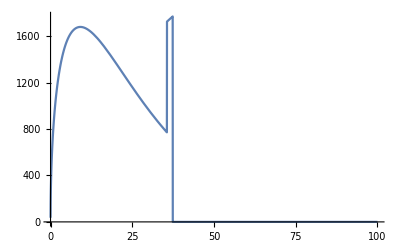

```mathematica
Plot[diskvelocity[r],{r,0,100}]
```